```mathematica
TransmissionCost[h_,x_,y_,pow_]:=1/((h^2+x^2+y^2)^(pow/2));
Table[Plot3D[TransmissionCost[5,x,y,pow], {x,-15,15},{y,-15,15},PlotRange->All,PerformanceGoal->"Quality"],{pow,{2,3,4}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*Plot the electric field of an electric dipole*)
Clear[pLoc]

efield[x_,y_,px_,py_,θ_,len_]:=
-1/(((px-x-len Cos[θ])^2+(py-y-len Sin[θ])^2)^2) (*repulsive force*)+(1/2)/(((px-x+len Cos[θ])^2+(py-y+len Sin[θ])^2)^2)(*attractive force*)
```

```mathematica
D[efield[x,y,px,py,θ,len],x]
D[efield[x,y,px,py,θ,len],y]
```

-(4 (px-x-len Cos[θ]))/(((px-x-len Cos[θ])^2+(py-y-len Sin[θ])^2)^3)+(2 (px-x+len Cos[θ]))/(((px-x+len Cos[θ])^2+(py-y+len Sin[θ])^2)^3)

-(4 (py-y-len Sin[θ]))/(((px-x-len Cos[θ])^2+(py-y-len Sin[θ])^2)^3)+(2 (py-y+len Sin[θ]))/(((px-x+len Cos[θ])^2+(py-y+len Sin[θ])^2)^3)

```mathematica
VectorEfield[x_,y_,px_,py_,θ_,len_]:= 
Normalize[{-(4 (px-x-len Cos[θ]))/(((px-x-len Cos[θ])^2+(py-y-len Sin[θ])^2)^3)+(2 (px-x+len Cos[θ]))/(((px-x+len Cos[θ])^2+(py-y+len Sin[θ])^2)^3),-(4 (py-y-len Sin[θ]))/(((px-x-len Cos[θ])^2+(py-y-len Sin[θ])^2)^3)+(2 (py-y+len Sin[θ]))/(((px-x+len Cos[θ])^2+(py-y+len Sin[θ])^2)^3)}];
Manipulate[Module[{px=1,py=1},
Show[{VectorPlot[VectorEfield[x,y,px,py,θ,len],{x,-5,5},{y,-5,5}],
Graphics[{
Red,Disk[{ (px+len Cos[θ]),(py+len Sin[θ] )},1/2],
Green,Disk[{ (px-len Cos[θ]),(py-len Sin[θ] )},1/2]
}]}]],{θ,-π,π},{len,1/8,2}]
```

```mathematica
Idea: make it a function of r and θ
```

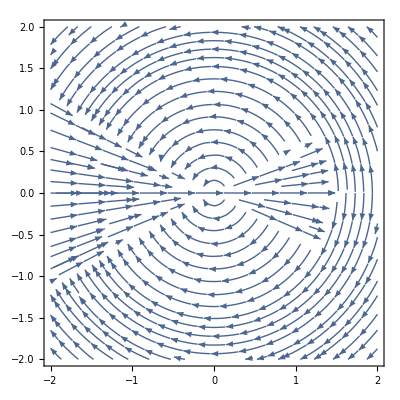

```mathematica
StreamPlot[θ=ArcTan[x,y];r = √(x^2+y^2);
Piecewise[{
{{Cos[θ],Sin[θ]},Abs[θ]<1/6π&& r<3/2},

{{-Cos[θ],Sin[-θ]},Abs[θ]>5/6π },

{{Cos[θ+π/2],Sin[θ+π/2]},θ>0},
{{Cos[θ-π/2],Sin[θ-π/2]},θ<0}

}],{x,-2,2},{y,-2,2},StreamPoints->Fine,(*VectorPoints->50,*)
PlotRange->All
]
```